#### Uniform density phase function (Axilens)

```mathematica
(*In this case everything is real, makes math faster*)
$Assumptions=_Symbol∈Reals
```

_Symbol∈Reals

Focus depth as a function of radius for a uniform laser intensity, Ic, extending from d2-d3, created by a flat top laser intensity of I0, incident on an annulus radius r1-r2. ϕp is the r derivative of the phase given by dϕ/dr=-Sin(θ)=r/√(r^2+(z(r))^2). a=(π I_0)/I_c=(d_3-d_2)/(r_2^2-r_1^2)and D=d_2-ar_1^2.

```mathematica
z[r_]:=a r^2+d;
ϕp[r_]:=-r/(√(r^2+z[r]^2));
```

```mathematica
Assuming[r>r1&&d>0&&a>0,∫_r1^r ϕp[rp] ⅆrp]
```

-Log[(1+2 a (d+a r^2+√(r^2+(d+a r^2)^2)))/(1+2 a (d+a r1^2+√(r1^2+(d+a r1^2)^2)))]/(2 a)

We can drop the denominator in the log. It is a constant and thus can be removed from the phase. This result matches that of Sochacki et al. 1992.

```mathematica
ϕ[r_]:=-1/(2 a) Log[1+2 a (D+a r^2+√(r^2+(D+a r^2)^2))];
```

In the paraxial approximation we can replace sin(θ) with tan(θ)=r/z in which case we get

```mathematica
ϕp[r_]:=r/z[r];
Assuming[r>r1&&d2>0&&r1>0&&I0>0&&Ic>0,∫_r1^r ϕp[rp] ⅆrp]
```

(Ic (-Log[d2 Ic]+Log[d2 Ic+I0 π (r-r1) (r+r1)]))/(2 I0 π)

#### Gaussian ramp phase function

First we need to invert the ADK ionization model which ends up giving the Lambert (ProductLog) function.

```mathematica
Solve[A==-e^n ⅇ^(-a/e),e]
```

{{e→a/(n ProductLog[(a (-A)^(-1/n))/n])}}

```mathematica
Iz[z_]:=G/ProductLog[β (-1/η Log[1-0.99 Exp[(-(z-d2)^2)/(2 σ^2)]])^(-β/a)]^2;
```

```mathematica
Assuming[zr>d1&&d1>0&&d2>0&&β>0&&η>0&&σ>0&&a>0&&d2>d1,∫_d1^zr Iz[z] ⅆz]
```

∫_d1^zr (1.55255×10^22)/(ProductLog[(1.6819×10^159)/((-Log[1-ⅇ^(-22.2222 (-1.+z)^2)])^8.26533)]^2)ⅆz

As expected this does not seem to have an analytic solution. Lets try plotting Iz with some representative constants.

```mathematica
c=3.00*^8;
n=1.0;
ϵ0=8.854*^-12;
ℏ=1.055*^-34;
e=1.602*^-19;
me=9.109*^-31;
ξi=15.426;
Z=1;
d2=1.0;
σ=0.15;
τp=50.0*^-15;
ns=3.69 Z/ξi^(1/2)
a=2^(5/2)/(3 ℏ) √(e me) ξi^(3/2)
η=(3 √e)/(√(2^3 π me)) 4^ns/(ns Gamma[2 ns]) τp/ξi^(1/2) (3 a)^(2 ns-1)
β=a/(2 (1-ns))
G=(c n ϵ0 β^2)/2
```

0.939506

4.13664×10^11

559.586

3.41907×10^12

1.55255×10^22

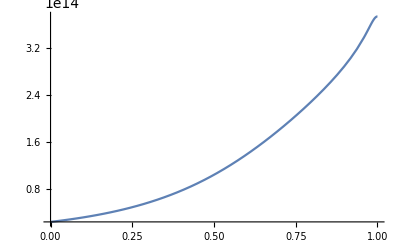

```mathematica
Plot[Iz[z]/10^4,{z,0,1}, PlotRange->Full]
```

It looks faintly parabolic, lets try series expanding it about 0 in z. As it ends up the higher order terms still matter a lot

1.03739×10^14+3.09572×10^14 (z-0.5)+3.88026×10^14 (z-0.5)^2+5.17876×10^13 (z-0.5)^3-5.22402×10^14 (z-0.5)^4-2.59031×10^14 (z-0.5)^5+O[z-0.5]^6

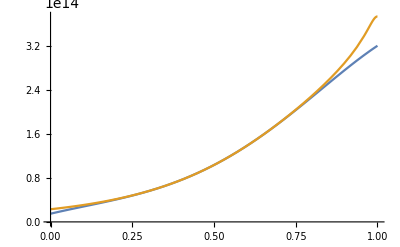

```mathematica
sIz=Series[Iz[z]/10^4,{z,0.5,5}]
Plot[{Iz[z]/10^4,Evaluate[Normal[sIz]]},{z,0,1}]
```

Ends up the terms don’t die off, I didn’t think this would work, but worth a try. Lets examine the argument of the Lambert W function (ProductLog) and see if we can expand the special function at all. The minimum value will be at z=d2 and it is:

```mathematica
β (-1/η Log[1-0.99 Exp[(-(d2-d2)^2)/(2 σ^2)]])^(-β/a)
```

5.80737×10^29

After using the asymptotic form of the W function:

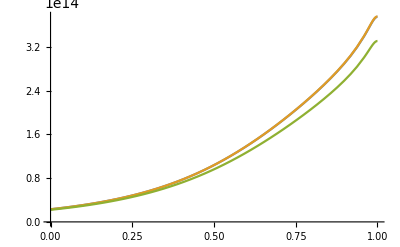

```mathematica
Iza[z_]:=G/(Log[β (-1/η Log[1-0.99 Exp[(-(z-d2)^2)/(2 σ^2)]])^(-β/a)]-Log[Log[β (-1/η Log[1-0.99 Exp[(-(z-d2)^2)/(2 σ^2)]])^(-β/a)]])^2;
Iza1[z_]:=G/(Log[β (-1/η Log[1-0.99 Exp[(-(z-d2)^2)/(2 σ^2)]])^(-β/a)])^2;
Plot[{Iz[z]/10^4,Iza[z]/10^4,Iza1[z]/10^4},{z,0,1}]
```

```mathematica
Assuming[zr>d1&&d1>0&&d2>0&&β>0&&η>0&&σ>0&&a>0&&d2>d1,∫_d1^zr Iza[z] ⅆz]
```

∫_d1^zr (1.55255×10^22)/((Log[(1.76166×10^35)/((-Log[1-0.99 ⅇ^(-22.2222 (-1.+z)^2)])^8.26533)]-Log[Log[(1.76166×10^35)/((-Log[1-0.99 ⅇ^(-22.2222 (-1.+z)^2)])^8.26533)]])^2)ⅆz

Still not integrable. Lets try series expanding the inner logarithm

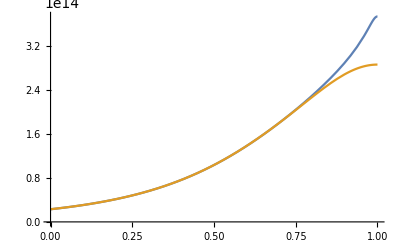

```mathematica
Izae[z_]:=G/(Log[β (-1/η (-0.99 Exp[(-(z-d2)^2)/(2 σ^2)]-0.5 0.99^2 Exp[(-(z-d2)^2)/σ^2]))^(-β/a)]-Log[Log[β (-1/η (-0.99 Exp[(-(z-d2)^2)/(2 σ^2)]-0.5 0.99^2 Exp[(-(z-d2)^2)/σ^2]))^(-β/a)]])^2;
Plot[{Iz[z]/10^4,Izae[z]/10^4},{z,0,1}]
```

I have no idea where to go with further approximations from here. I’m not sure their is a good analytic solution to this problem so numerical solutions to the differential equations instead.